## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380";
```

```mathematica
Directory[]
```

/home/chengling

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
saveFolderLT="/home/chengling/Research/Project/Cell/glassyDynamics/longtimeSimulation/N4096/";
```

```mathematica
TlistLongest={0.00222222 ,0.00210526, 0.002, 0.00190476 ,0.00181818};
```

```mathematica
1/TlistLongest
```

{450.,475.001,500.,525.001,550.001}

```mathematica
N[1/{450,475,500,525,550}]
```

{0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TstringLongest=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistLongest
```

{0.00222222,0.00210526,0.00200000,0.00190476,0.00181818}

```mathematica
wtlistLongest={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststringLongest=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{0.000000,50000.000000,60000.000000,70000.000000,80000.000000,90000.000000,100000.000000}

```mathematica
SISFLongest=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLongest[[1]],"_waitingTime",wtliststringLongest[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
overlapLongest=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLongest[[5]],"_waitingTime",wtliststringLongest[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
SISFLT[[1,1,1]]
```

1.

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLongest[[2]],"_waitingTime",wtliststringLongest[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,7}];
```

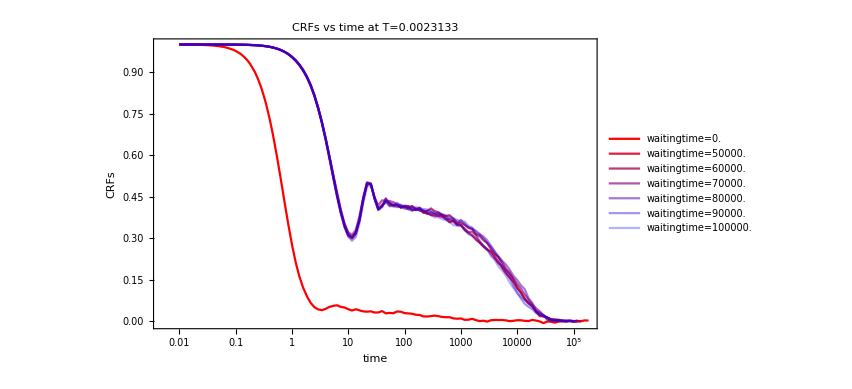

```mathematica
CRFswaitTimeLongest=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISFLongest[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLongest[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRFswaitTimeLT.jpeg",CRFswaitTimeLT,ImageResolution->600];
```

General::stop: Further output of Part::partw will be suppressed during this calculation.

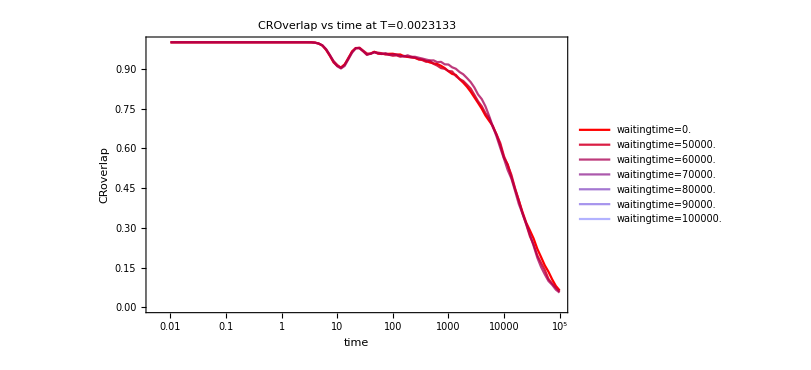

```mathematica
CRoverlapwaitTimeLongest=ListLogLinearPlot[Table[Table[{timeLongest[[t]],Mean[Table[overlapLongest[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest]}],{wt,7}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CROverlap vs time at T=0.0023133",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlistLongest[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlapLongest=Table[Table[Import[StringJoin[saveFolderLT,"overlap_N4096_p3.8000_T",TstringLongest[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLongest]}];
```

```mathematica
SISFLongest=Table[Table[Import[StringJoin[saveFolderLT,"SISF_N4096_p3.8000_T",TstringLongest[[T]],"_waitingTime100000.000000_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[TlistLongest]}];
```

```mathematica
CRoverlapMeanLongest=Table[Table[Mean[Table[overlapLongest[[T,i,2,rec]],{i,3}]],{rec,Length[overlapLongest[[T,1,1]]]}],{T,Length[TlistLongest]}];
```

```mathematica
CRSISFMeanLongest=Table[Table[Mean[Table[SISFLongest[[T,i,2,rec]],{i,3}]],{rec,Length[SISFLongest[[T,1,1]]]}],{T,Length[TlistLongest]}];
```

```mathematica
testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",TstringLongest[[2]],"_waitingTime",wtliststringLongest[[7]],"_idx1.nc"],"Data"];timeLongest=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.09,0.1,0.12,0.14,0.16,0.18,0.22,0.25,0.29,0.34,0.4,0.46,0.54,0.63,0.74,0.86,1.,1.17,1.36,1.58,1.85,2.15,2.51,2.93,3.41,3.98,4.64,5.41,6.31,7.36,8.58,10.,11.66,13.59,15.85,18.48,21.54,25.12,29.29,34.15,39.81,46.42,54.12,63.1,73.56,85.77,100.,116.59,135.94,158.49,184.78,215.44,251.19,292.86,341.45,398.11,464.16,541.17,630.96,735.64,857.7,1000.,1165.91,1359.36,1584.89,1847.85,2154.43,2511.89,2928.64,3414.55,3981.07,4641.59,5411.7,6309.57,7356.42,8576.96,10000.,11659.1,13593.6,15848.9,18478.5,21544.3,25118.9,29286.4,34145.5,39810.7,46415.9,54117.,63095.7,73564.2,85769.6,100000.}

```mathematica
CRoverlapMeanLongest[[1,50]]
```

0.961182

```mathematica
Log10[timeLongest[[52]]]
```

1.80003

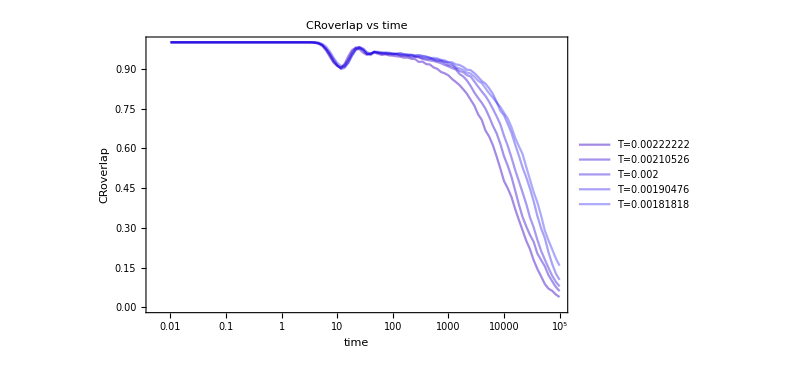

```mathematica
CRoverlapLongestPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRoverlapMeanLongest[[T,rec]]},{rec,Length[CRoverlapMeanLongest[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLongest]}],PlotStyle->redBluePlotConfig[Length[Tlist]+Length[TlistLT]+Length[TlistLongest]][[Length[Tlist]+Length[TlistLT];;]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
Table[{Normal[timeLongest[[rec]]],Normal[CRoverlapMeanLongest[[2,rec]]]},{rec,52,Length[timeLongest]}]
```

{{63.1,0.958822},{73.56,0.958171},{85.77,0.956543},{100.,0.955892},{116.59,0.955241},{135.94,0.952637},{158.49,0.951172},{184.78,0.947673},{215.44,0.951416},{251.19,0.945394},{292.86,0.943848},{341.45,0.937419},{398.11,0.934163},{464.16,0.931315},{541.17,0.929362},{630.96,0.925456},{735.64,0.921143},{857.7,0.914388},{1000.,0.909098},{1165.91,0.902832},{1359.36,0.897461},{1584.89,0.880452},{1847.85,0.871012},{2154.43,0.855957},{2511.89,0.835124},{2928.64,0.810547},{3414.55,0.790202},{3981.07,0.771729},{4641.59,0.749674},{5411.7,0.718994},{6309.57,0.685221},{7356.42,0.65682},{8576.96,0.617025},{10000.,0.57015},{11659.1,0.534505},{13593.6,0.493245},{15848.9,0.441488},{18478.5,0.388835},{21544.3,0.341471},{25118.9,0.30542},{29286.4,0.273275},{34145.5,0.247477},{39810.7,0.203125},{46415.9,0.178874},{54117.,0.155518},{63095.7,0.121582},{73564.2,0.0986328},{85769.6,0.0767415},{100000.,0.0612793}}

```mathematica
fitsCRoverlapLongest=Table[NonlinearModelFit[Table[{Normal[timeLongest[[rec]]],Normal[CRoverlapMeanLongest[[T,rec]]]},{rec,52,Length[timeLongest]}],{stretchedExp[t,G,τ,β],{1.0>β>0.2,1>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLongest]}];
```

```mathematica
fitsCRoverlapLongest["BestFitParameters"]
```

{FittedModel[0.973606 ⅇ^(-0.000578591 t^0.765277)],FittedModel[0.976955 ⅇ^(-0.000322894 t^0.801778)],FittedModel[0.965694 ⅇ^(-0.000137269 t^0.865234)],FittedModel[0.961696 ⅇ^(-0.000064361 t^0.912167)],FittedModel[0.962681 ⅇ^(-0.0001252 t^0.836894)]}[BestFitParameters]

```mathematica
tauCRoverlapfitsLongest=Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLT]}]
```

{17008.4,22594.2,29109.1,39352.1,46020.2}

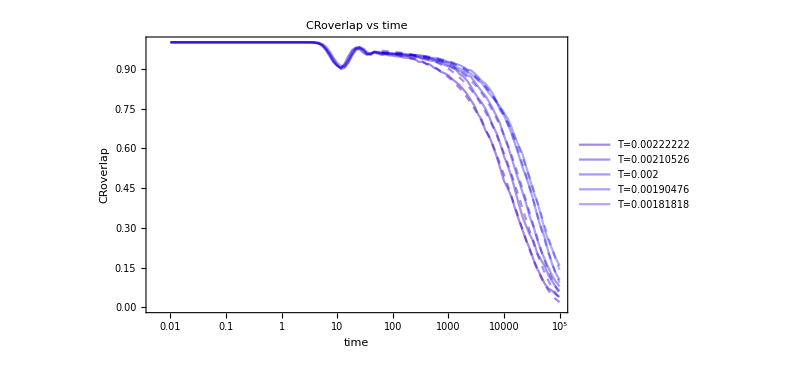

```mathematica
Show[CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

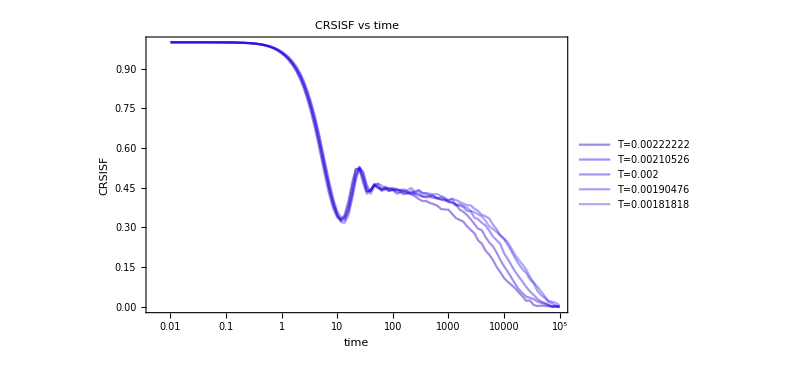

```mathematica
CRSISFLongestPlot=ListLogLinearPlot[Table[Table[{timeLT[[rec]],CRSISFMeanLongest[[T,rec]]},{rec,Length[CRoverlapMeanLongest[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLT]}],PlotStyle->redBluePlotConfig[Length[TlistAllT]][[Length[Tlist]+Length[TlistLT];;]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitsCRSISFLongest=Table[NonlinearModelFit[Table[{Normal[timeLongest[[rec]]],Normal[CRSISFMeanLongest[[T,rec]]]},{rec,52,Length[timeLongest]}],{stretchedExp[t,G,τ,β],{0.81>β>0.2,0.5>G>0,τ>3}},{G,τ,β},t],{T,Length[TlistLongest]}];
```

```mathematica
fitsCRSISFLongest
```

{FittedModel[0.448606 ⅇ^(-0.000903807 t^(«19»))],FittedModel[0.457386 ⅇ^(-0.000607876 t^(«19»))],FittedModel[0.45083 ⅇ^(-0.000458899 t^(«19»))],FittedModel[0.452285 ⅇ^(-0.00034579 t^(«19»))],FittedModel[0.449566 ⅇ^(-0.000391055 t^(«19»))]}

```mathematica
tauCRSISFfitsLongest=Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLongest]}]
```

{6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
Length[TlistLongest]
```

5

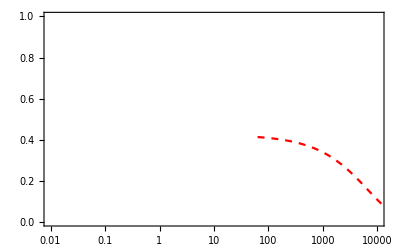
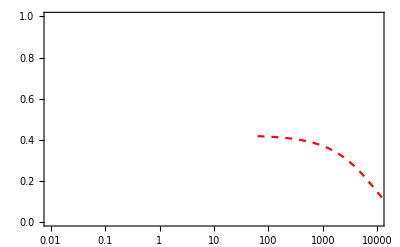
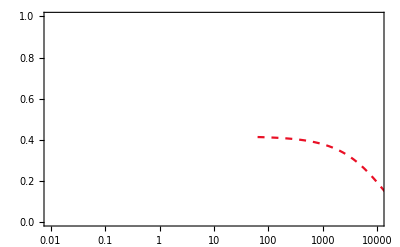
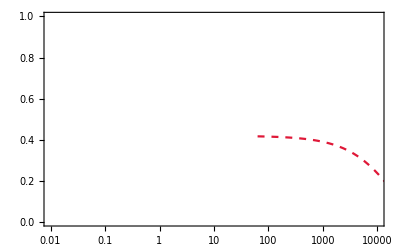
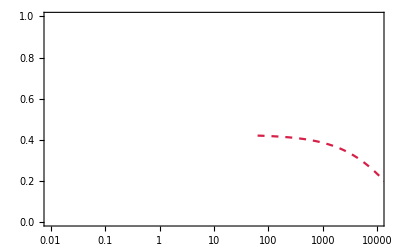

```mathematica
Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLongest[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T]]}],{T,Length[TlistLongest]}]
```

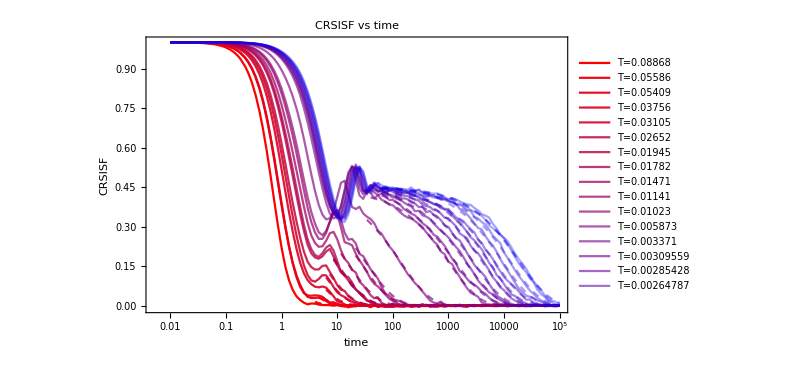

```mathematica
Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

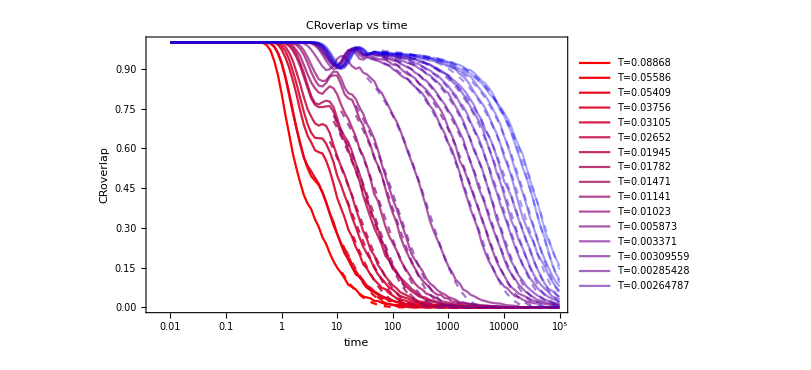

```mathematica
Show[CRoverlapSTLTwithFitPlot,CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRoverlap_p380.jpeg",Show[CRoverlapSTLTwithFitPlot,CRoverlapLongestPlot,Table[LogLinearPlot[fitsCRoverlapLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

```mathematica
tauCRoverlapAllT=Join[tauCRoverlapfits,tauCRoverlapfitsLT,tauCRoverlapfitsLongest]
```

{3.16039,6.7635,6.75448,12.5106,17.4891,23.0389,38.8819,42.9591,64.5399,101.84,125.531,436.846,2732.95,3582.02,5140.15,7160.55,10064.4,13246.9,17008.4,22594.2,29109.1,39352.1,46020.2}

```mathematica
tauCRSISFAllT=Join[tauCRSISFfits,tauCRSISFfitsLT,tauCRSISFfitsLongest]
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
TlistAllT=Join[Tlist,TlistLT,TlistLongest];
```

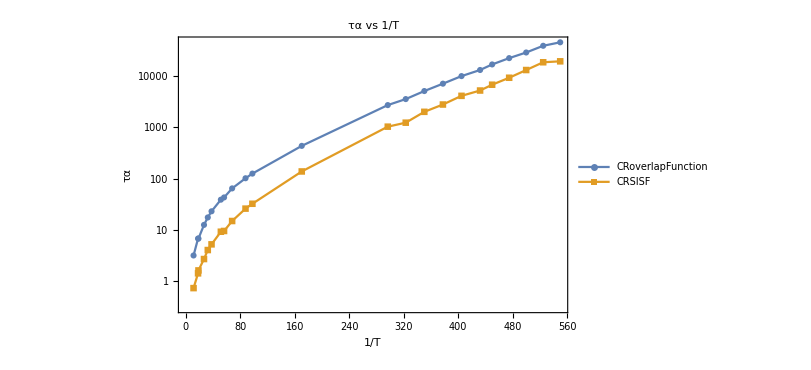

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

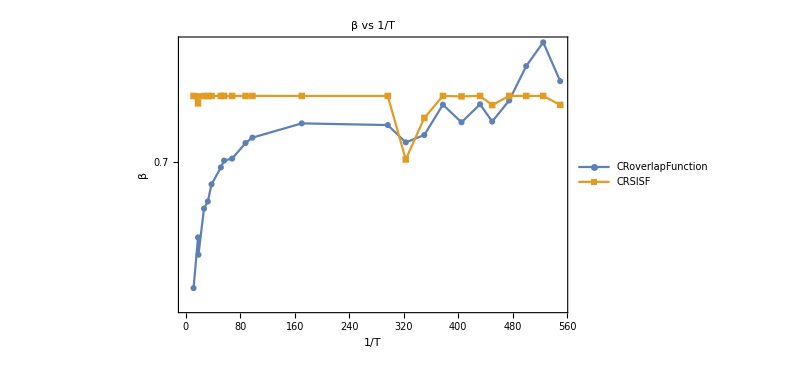

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

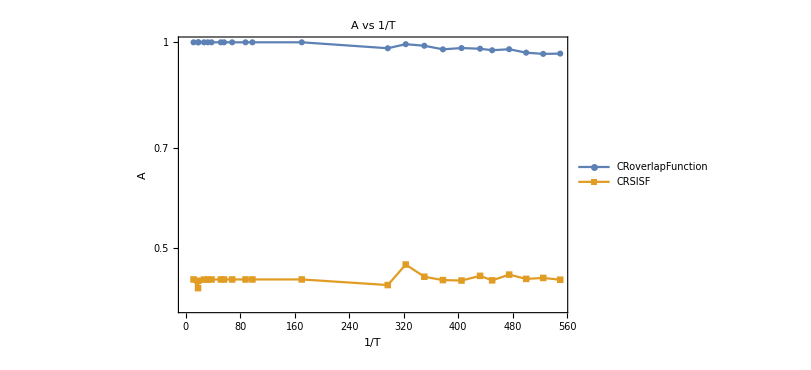

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

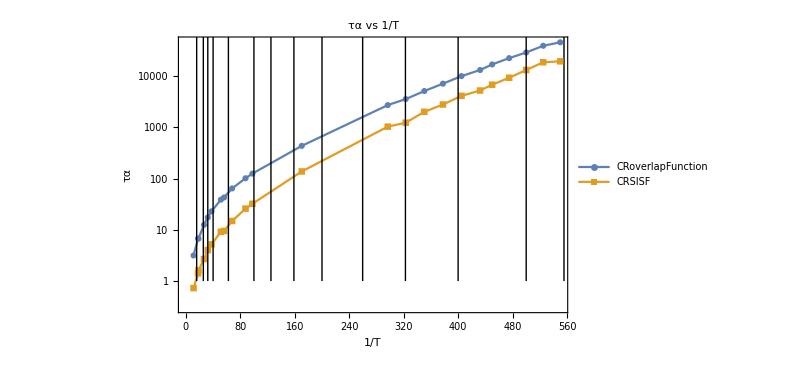

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

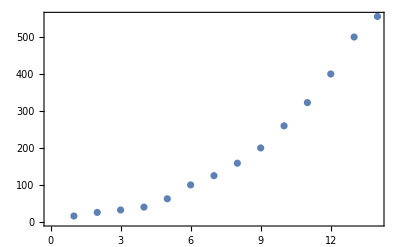

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16